```mathematica
psir[n_,finf_,cl_,alpha_]:=finf+cl*Exp[-alpha*n]
```

```mathematica
g[n1_,n2_,n3_,alpha_]=(psir[n1,finf,cl,alpha]-psir[n2,finf,cl,alpha])/(psir[n1,finf,cl,alpha]-psir[n3,finf,cl,alpha])//Simplify
```

(ⅇ^(-alpha n2) (ⅇ^(alpha n1)-ⅇ^(alpha n2)))/(-1+ⅇ^(alpha (n1-n3)))

```mathematica
psirn1=-8.8634055426379366*10^-05
```

-0.0000886341

```mathematica
psirn2=-8.8634059283183525*10^-05
```

-0.0000886341

```mathematica
psirn3=-8.8634062152950001*10^-05
```

-0.0000886341

```mathematica
h=(psirn1-psirn2)/(psirn1-psirn3)
```

0.573369

```mathematica
alpharule=NSolve[g[36,40,44,alpha]-h,alpha,Reals]
```

{{alpha→0.0739021}}

```mathematica
c[n1_,n2_,n3_,alpha_]=(psir[n1,finf,cl,alpha]-psir[n2,finf,cl,alpha])/(Exp[-alpha*n1]-Exp[-alpha*n2])//Simplify
```

cl

```mathematica
cnum=.
```

```mathematica
cnum=(psirn1-psirn2)/(Exp[-alpha*36]-Exp[-alpha*40])/.alpharule
```

{2.15551×10^-10}

```mathematica
cnumrule=cl->cnum
```

cl→{2.15551×10^-10}

```mathematica
Solve[psirn==psir[n3,finf,cl,alpha],finf]
```

{{finf→ⅇ^(-alpha n3) (-cl+ⅇ^(alpha n3) psirn)}}

```mathematica
finfrule=Solve[psirn3==psir[44,finf,cl,alpha]/.alpharule/.cnumrule, finf]
```

{{finf→-0.0000886341}}

```mathematica
FullForm[finf]/.finfrule
```

{-0.0000886341}

```mathematica
psirdata = {-8.8633901417211114*10^-05,-8.8633975615181649*10^-05,-8.863401088985772*10^-05,-8.8634030396720086*10^-05,-8.8634042286234415*10^-05,-8.8634050051831568*10^-05,-8.8634055426379366*10^-05,-8.8634059283183525*10^-05,-8.8634062152950001*10^-05}
```

{-0.0000886339,-0.000088634,-0.000088634,-0.000088634,-0.000088634,-0.0000886341,-0.0000886341,-0.0000886341,-0.0000886341}

```mathematica
orderdata={12, 16, 20, 24, 28, 32, 36, 40, 44}
```

{12,16,20,24,28,32,36,40,44}

```mathematica
unscaledlistdata={orderdata,psirdata}
```

{{12,16,20,24,28,32,36,40,44},{-0.0000886339,-0.000088634,-0.000088634,-0.000088634,-0.000088634,-0.0000886341,-0.0000886341,-0.0000886341,-0.0000886341}}

```mathematica
l[order_]=finf/.finfrule[[1]]
```

-0.0000886341

```mathematica
unscaledtransdata=Transpose[unscaledlistdata]
```

{{12,-0.0000886339},{16,-0.000088634},{20,-0.000088634},{24,-0.000088634},{28,-0.000088634},{32,-0.0000886341},{36,-0.0000886341},{40,-0.0000886341},{44,-0.0000886341}}

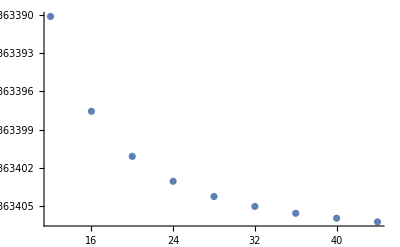

```mathematica
p1=ListPlot[unscaledtransdata]
```

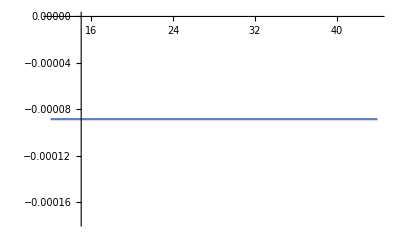

```mathematica
p2=Plot[finf/.finfrule[[1]],{x,12,44}]
```

```mathematica
Show[p1,p2]
```

-Graphics-

```mathematica
listdata={orderdata,Flatten[Abs[psirdata-finf/.finfrule]]}
```

{{12,16,20,24,28,32,36,40,44},{1.69079×10^-10,9.48815×10^-11,5.96068×10^-11,4.00999×10^-11,2.82104×10^-11,2.04448×10^-11,1.50703×10^-11,1.12135×10^-11,8.34371×10^-12}}

```mathematica
transdata=Transpose[listdata]
```

{{12,1.69079×10^-10},{16,9.48815×10^-11},{20,5.96068×10^-11},{24,4.00999×10^-11},{28,2.82104×10^-11},{32,2.04448×10^-11},{36,1.50703×10^-11},{40,1.12135×10^-11},{44,8.34371×10^-12}}

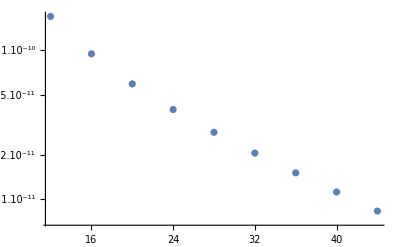

```mathematica
ListLogPlot[transdata]
```